```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

{KernelObject[1,local],KernelObject[2,local]}

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[235,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[10^(-3)/lc,MachinePrecision];(*период ондулятора 10 мкм*)
kdip=SetPrecision[0,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 0.

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=25;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
```

```mathematica
mpp=SetPrecision[938.27 10^6,MachinePrecision];(*масса протона в эВ*)
Mmol=18 12+19+14;(*относительная молярная масса C18H19N*)
Zn=18 6+19+7;(*число электронов в молекуле*)
nmm=5.60958 10^(32)/(mpp Mmol);(*концентрация молекул при плотности массы 1 g/cm^3 в 1/cm^3*)
ωp=Sqrt[4 Pi α Zn nmm lc^3];(*плазменная частота в естественных единицах*)
ϵpp[k0_]=1-1/3 ωp^2/k0^2;(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=1-ωp^2/k0^2;(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика q: ",qc mee, " эВ"]
Print["Толщина пластины холестерика Lz: ",Lz lc 10^4, " мкм"]
Print["Плазменная частота: ",ωp mee," эВ,  ",2.42 10^(14) ωp mee," Гц"]
Module[{xx=30/mee},(*предполагаемая энергия фотона*)
Print["Анизотропия de: ",dec[xx]];
Print["Параметр ВКБ: ", (dec[xx] ϵpp[xx]^(1/2) xx/(4 qc))^2]]
```

Волновой вектор холестерика q: 0.774583 эВ

Толщина пластины холестерика Lz: 20. мкм

Плазменная частота: 21.0523 эВ,  5.09467×10^15 Гц

Анизотропия de: -0.39277

Параметр ВКБ: 12.089

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={0,0,zo+βp t};
v[t_]={0,0,βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=(√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1+(kp^2 (-(4 (√(k0s (de (de k0s+8)+16))+4))-de (de k0s+√(k0s (de (de k0s+8)+16))+4)))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)));(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=√((de k0s)/2-1/2 √(k0s (de (de k0s+8)+16))+k0s+1)+1+(-de (-de k0s+√(k0s (de (de k0s+8)+16))-4)-4 √(k0s (de (de k0s+8)+16))+16)/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))) kp^2;(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinComb]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{xps0,xmsm2,xps2,xms0,xpsm2,xmsm4,yps0,ymsm2,yps2,yms0,ypsm2,ymsm4,xms2,xpsm4,yms2,ypsm4,tf,ts,r,apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm},

n3i=1/n3;

xps0=1;
xmsm2=-(2 (-((√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1)^2+(de k0s)/2+k0s))/(de k0s)+kp^2 ((√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4)/(2 de k0s^2)-(2 (((4 (√(k0s (de (de k0s+8)+16))+4)+de (de k0s+√(k0s (de (de k0s+8)+16))+4)) (√2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+2))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)))-de/4-1))/(de k0s));
xps2=-kp^2 ((de (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xms0=-kp^2 (((de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4) (√(k0s (de (de k0s+8)+16))+6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xpsm2=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20) (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xmsm4=-kp^2 ((de(de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));

(*медленная волна*)
yps0=1;
ymsm2=-(2 (-1/4 (√(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+2)^2+(de k0s)/2+k0s))/(de k0s)+(kp^2 (k0s (-(√2 de^2 k0s)+√2 de √(k0s (de (de k0s+8)+16))-4 de √((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)-4 √2 (3 de+4))+4 (√2 √(k0s (de (de k0s+8)+16))+√(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)))))/(2 de k0s^2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)));
yps2=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));
yms0=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20) (-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ypsm2=-kp^2 (((-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4) (√(k0s (de (de k0s+8)+16))+6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ymsm4=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));

xmsm2=If[xmsm2∈Reals,xmsm2,0];(*коэффициенты должны быть вещественными*)
xps2=If[xps2∈Reals,xps2,0];
xms0=If[xms0∈Reals,xms0,0];
xpsm2=If[xpsm2∈Reals,xpsm2,0];
xmsm4=If[xmsm4∈Reals,xmsm4,0];
ymsm2=If[ymsm2∈Reals,ymsm2,0];(*коэффициенты должны быть вещественными*)
yps2=If[yps2∈Reals,yps2,0];
yms0=If[yms0∈Reals,yms0,0];
ypsm2=If[ypsm2∈Reals,ypsm2,0];
ymsm4=If[ymsm4∈Reals,ymsm4,0];

xms2=0;xpsm4=0;yms2=0;ypsm4=0;(*зануляем высшие поправки*)

tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=1/rff^2;(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm при z=0*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
apss=ts(yps0+yps2 r+ypsm2/r);
amss=ts (yms0+ymsm2/r+ymsm4/r^2);
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm сопряженное при z=0*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
amscs=1/ts (yps0 +yps2/r+ypsm2 r);
apscs=1/ts(yms0+ymsm2 r+ymsm4 r^2);
(*-I K dz U11 при z=0*)
rapfs=tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2)/r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramfs=tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2)/r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4)/r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4)));
rapss=ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2)/r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
ramss=ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2)/r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4)/r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));
(*U21*)
ramfcs=-1/tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2)/r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapfcs=-1/tf ((pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2) r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4) r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4))));
ramscs=-1/ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2)/r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
rapscs=-1/ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2) r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4) r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
(*ach=LinearSolve[um,gv];*)
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];
{norm,ach,al,{xmsm2,xps2,xms0,xpsm2,xmsm4},{ymsm2,yps2,yms0,ypsm2,ymsm4}}](*выдает ответ в виде списка*)
```

```mathematica
ModeFun1[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,xmsm2_?NumberQ,xps2_?NumberQ,xms0_?NumberQ,xpsm2_?NumberQ,xmsm4_?NumberQ,pf_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{xps0,tf,r,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
xps0=1;
(*xms2=0;xpsm4=0;(*зануляем высшие поправки*)*)

tf=Exp[I pf tetb];r=rf1;(*фазовые множители*)

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm,3*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
a3fs=-kp/(2 k3b^2) tf ((pf xps0+(pf+2) xps2 r+(pf-2) xpsm2/r)+(pf xms0+(pf-2) xmsm2/r+(pf-4) xmsm4/r^2));
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm,3 сопряженное*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
a3fcs=kp/(2 k3b^2)/tf ((pf xps0+(pf+2) xps2/r+(pf-2) xpsm2 r)+(pf xms0+(pf-2) xmsm2 r+(pf-4) r^2xmsm4));

{{apfs rff,amfs/rff,a3fs},{apfcs rff,amfcs/rff,a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,ymsm2_?NumberQ,yps2_?NumberQ,yms0_?NumberQ,ypsm2_?NumberQ,ymsm4_?NumberQ,ps_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{yps0,ts,r,apss,amss,a3ss,amscs,apscs,a3scs},
yps0=1;
(*yms2=0;ypsm4=0;(*зануляем высшие поправки*)*)

ts=Exp[I ps tetb];r=rf1;(*фазовые множители*)

apss=ts (yps0+yps2 r+ypsm2/r);(*a_pm,3*)
amss=ts(yms0+ymsm2/r+ymsm4/r^2);
a3ss=-kp/(2 k3b^2) ts ((ps yps0+(ps+2) yps2 r+(ps-2) ypsm2/r)+(ps yms0+(ps-2) ymsm2/r+(ps-4) ymsm4/r^2));
amscs=1/ts (yps0+yps2/r+ypsm2 r);(*a_pm,3 сопряженное*)
apscs=1/ts (yms0+ymsm2 r+r^2ymsm4);
a3scs=kp/(2 k3b^2)/ts ((ps yps0+(ps+2) yps2/r+(ps-2) ypsm2 r)+(ps yms0+(ps-2) ymsm2 r+(ps-4) r^2ymsm4));

{{apss rff,amss/rff,a3ss},{apscs rff,amscs/rff,a3scs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,achli_,xxsl_,yysl_,pf_?NumberQ,ps_?NumberQ,k3b_?NumberQ]:=Module[{rfff,afrl,asrl,vpt,vmt,v3t,tet},
tet=qc x3[t]-ϕ;
rfff=Exp[2 I tet];(*фазовый множитель*)

afrl=ModeFun1[tet,kp,rff,xxsl[[1]],xxsl[[2]],xxsl[[3]],xxsl[[4]],xxsl[[5]],pf,k3b,rfff];
asrl=ModeFun2[tet,kp,rff,yysl[[1]],yysl[[2]],yysl[[3]],yysl[[4]],yysl[[5]],ps,k3b,rfff];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

```mathematica
BuildMPlot[k00_?NumberQ,npp_?NumberQ]:=Module[{llxts1,llxtsm1,tmxs1,tmxsm1},
llxts1=AmplTwistTab[1,k00,k00 npp];
llxtsm1=AmplTwistTab[-1,k00,k00 npp];
tmxs1=Table[{m,dProbabTwist[m,llxts1[[3]]]},{m,-mMax,mMax}];
tmxsm1=Table[{m,dProbabTwist[m,llxtsm1[[3]]]},{m,-mMax,mMax}];

{ListPlot[tmxs1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmxsm1,Frame->True,Axes->False,PlotRange->Full]}]
```

```mathematica
(*-------примеры-------*)
```

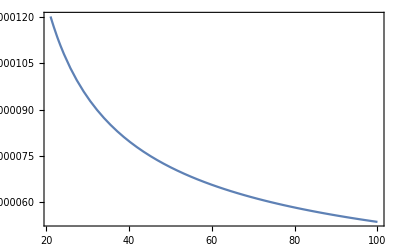
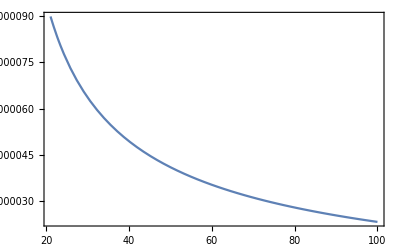
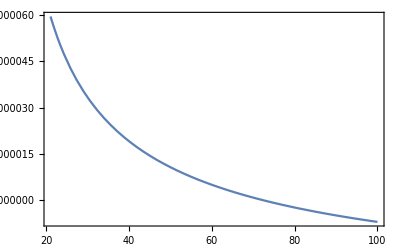
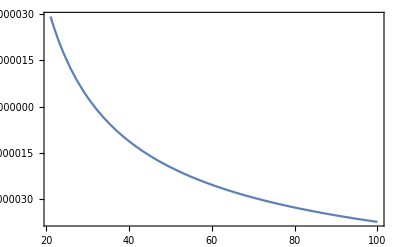

```mathematica
(*np = 1/100*)
{Plot[EqnSpecX[xx/mee,1/100,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/100,0],{xx,70}]
FindRoot[EqnSpecX[xx/mee,1/100,1],{xx,30}]
```

{xx→72.5465}

{xx→31.636}

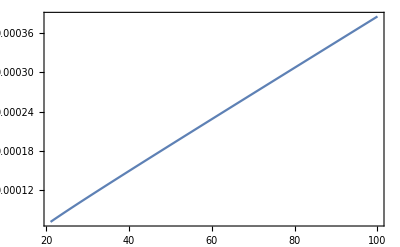
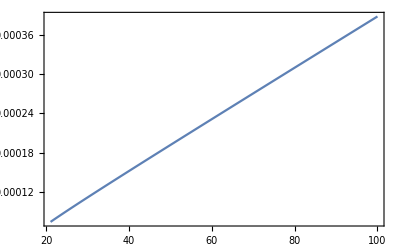
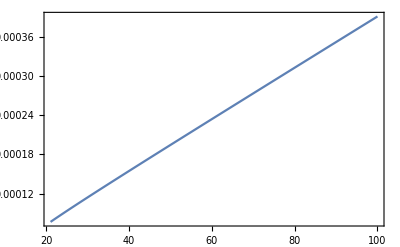
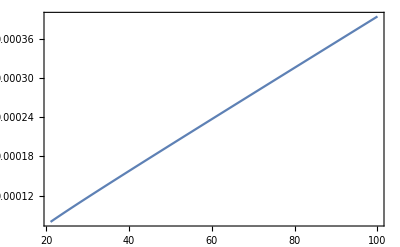

```mathematica
{Plot[EqnSpecTX[xx/mee,1/100,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/100,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/100,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/100,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

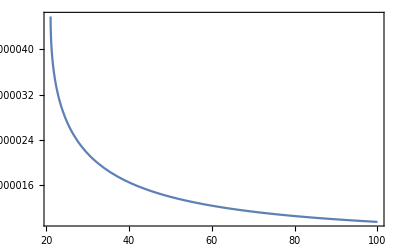
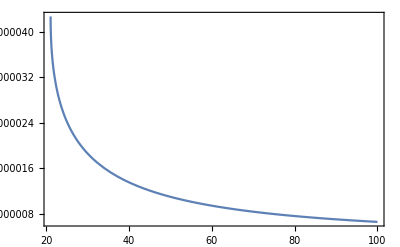
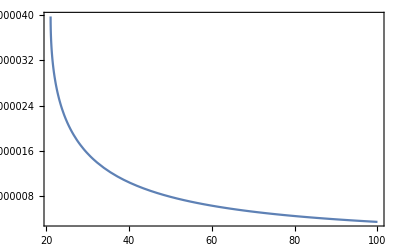
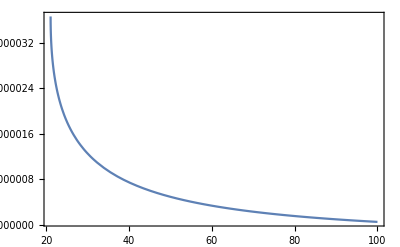

```mathematica
{Plot[EqnSpecY[xx/mee,1/100,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

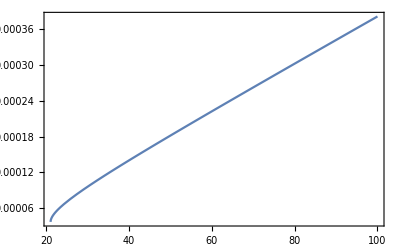
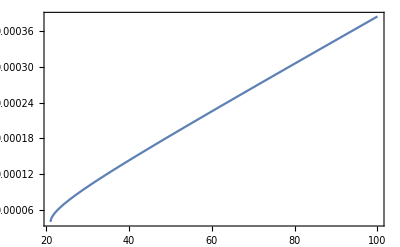
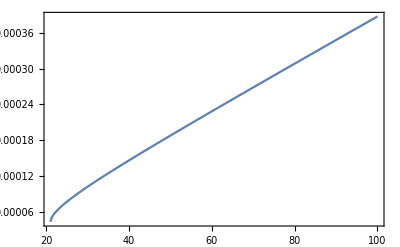
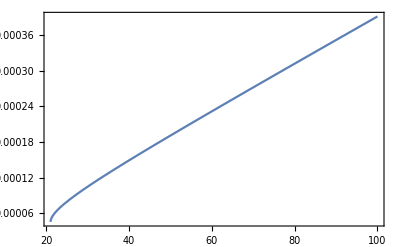

```mathematica
{Plot[EqnSpecTY[xx/mee,1/100,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/100,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/100,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/100,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
tk01s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/100,0]},{x,68,76,0.1}];
tk01sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/100,0]},{x,68,76,0.1}];
tk02s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/100,0]},{x,26,34,0.1}];
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/100,0]},{x,26,34,0.1}];
(*без пиков*)
```

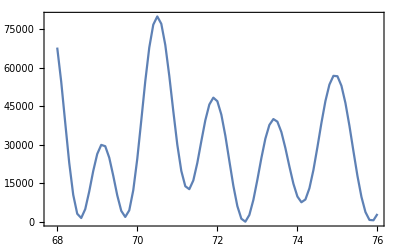
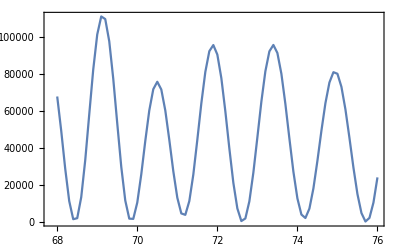
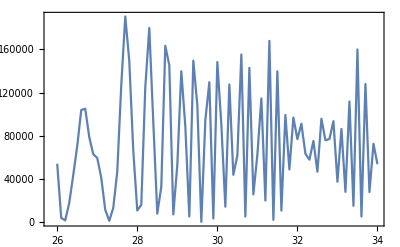
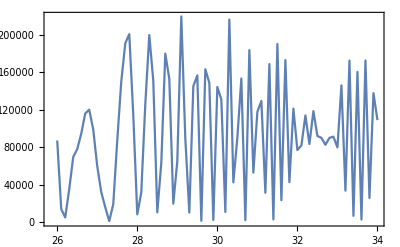

```mathematica
{ListLinePlot[tk01s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk01sm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk02s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]}
```

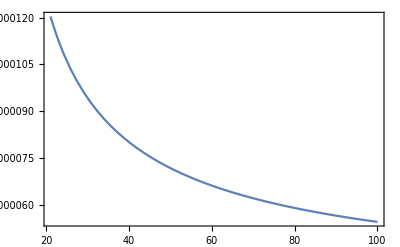
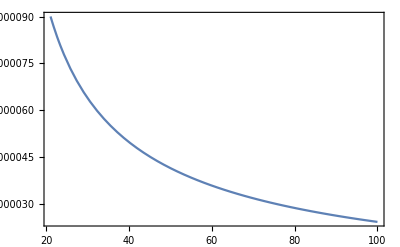
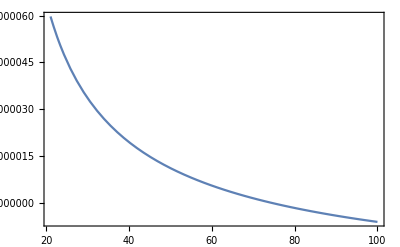
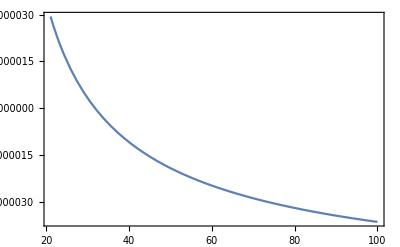

```mathematica
(*np = 1/30*)
{Plot[EqnSpecX[xx/mee,1/30,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/30,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/30,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/30,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/30,0],{xx,70}]
FindRoot[EqnSpecX[xx/mee,1/30,1],{xx,30}]
```

{xx→74.8289}

{xx→31.8363}

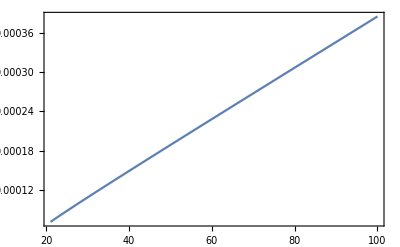
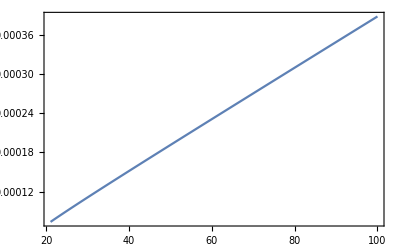
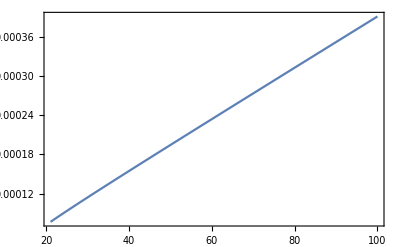
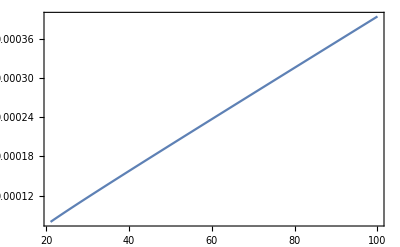

```mathematica
{Plot[EqnSpecTX[xx/mee,1/30,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/30,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/30,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/30,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

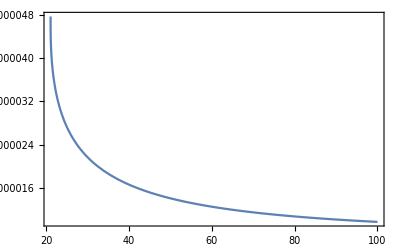
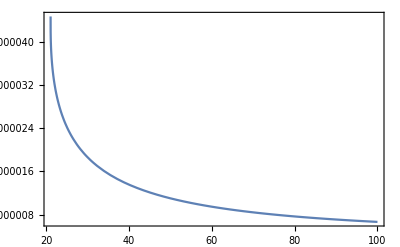
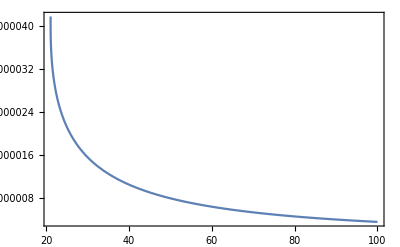
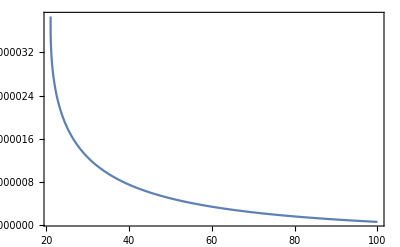

```mathematica
{Plot[EqnSpecY[xx/mee,1/30,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/30,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/30,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/30,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/30,1],{xx,100}]
```

{xx→118.279}

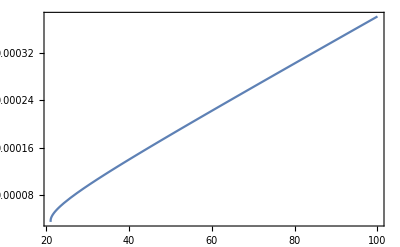
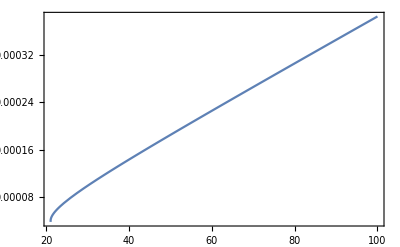
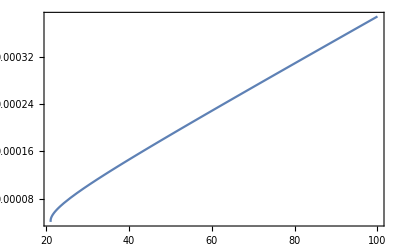
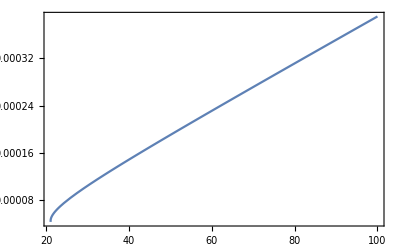

```mathematica
{Plot[EqnSpecTY[xx/mee,1/30,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/30,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/30,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/30,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
tk03s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/30,0]},{x,70,78,0.1}];
tk03sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/30,0]},{x,70,78,0.1}];
tk04s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/30,0]},{x,26,34,0.1}];
tk04sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/30,0]},{x,26,34,0.1}];
(*на первом графике что-то похожее на пик*)
```

```mathematica
tk09s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/30,0]},{x,114,122,0.1}];
tk09sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/30,0]},{x,114,122,0.1}];
```

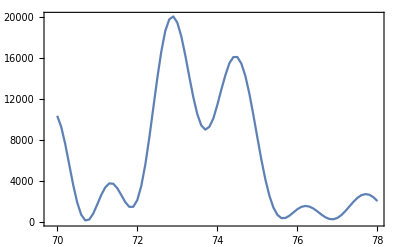
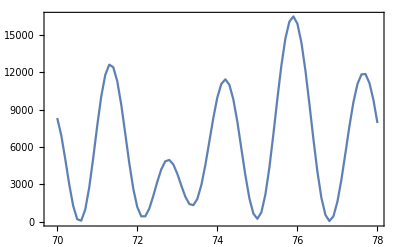
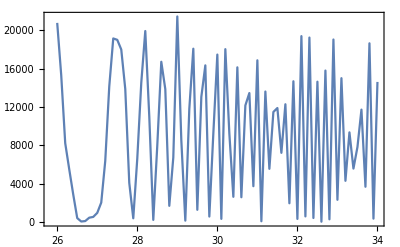
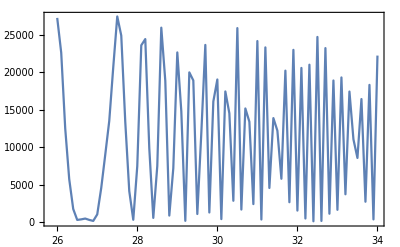
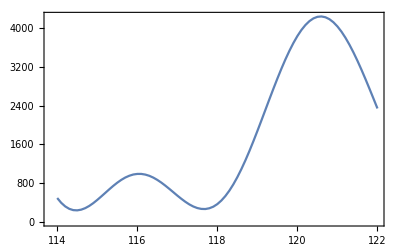
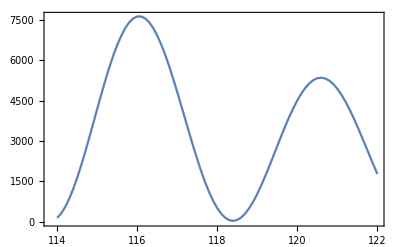

```mathematica
{ListLinePlot[tk03s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk03sm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk04s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk04sm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk09s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk09sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*хорошее распределение для s=1*)
```

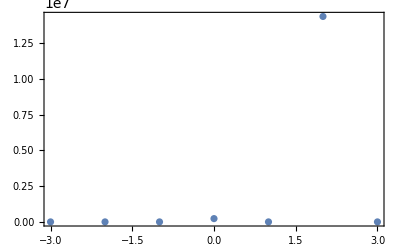
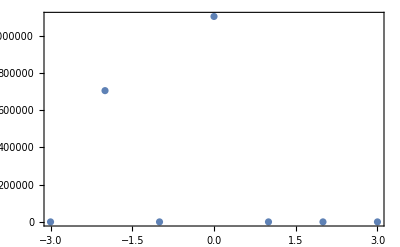

```mathematica
ll2ts1=AmplTwistTab[1,74.8/mee,74.8/mee/30];
ll2tsm1=AmplTwistTab[-1,74.8/mee,74.8/mee/30];
tm2s1=Table[{m,dProbabTwist[m,ll2ts1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,ll2tsm1[[3]]]},{m,-mMax,mMax}];
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*приемлемое распределение в левом пике для s=-1*)
```

```mathematica
ll3ts1=AmplTwistTab[1,72.9/mee,73/mee/30];
ll3tsm1=AmplTwistTab[-1,72.9/mee,73/mee/30];
```

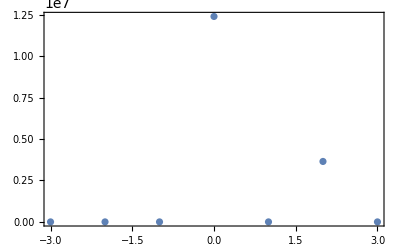
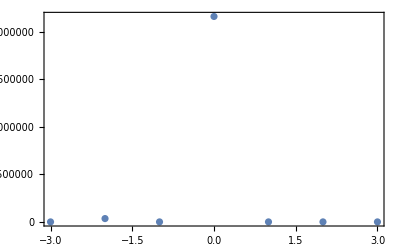

```mathematica
tm3s1=Table[{m,dProbabTwist[m,ll3ts1[[3]]]},{m,-mMax,mMax}];
tm3sm1=Table[{m,dProbabTwist[m,ll3tsm1[[3]]]},{m,-mMax,mMax}];
{ListPlot[tm3s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm3sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*плохое распределение в правом пике*)
```

```mathematica
ll4ts1=AmplTwistTab[1,74.4/mee,74.4/mee/30];
ll4tsm1=AmplTwistTab[-1,74.4/mee,74.4/mee/30];
```

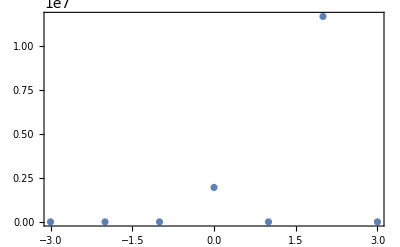
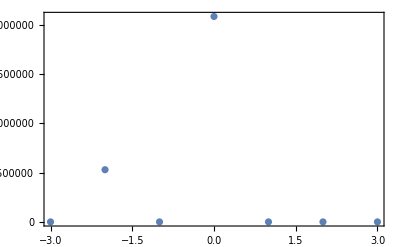

```mathematica
tm4s1=Table[{m,dProbabTwist[m,ll4ts1[[3]]]},{m,-mMax,mMax}];
tm4sm1=Table[{m,dProbabTwist[m,ll4tsm1[[3]]]},{m,-mMax,mMax}];
{ListPlot[tm4s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm4sm1,Frame->True,Axes->False,PlotRange->Full]}
```

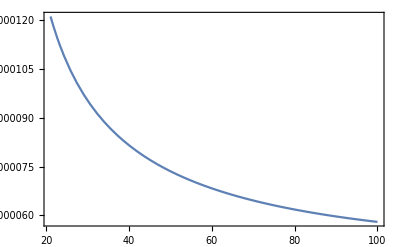
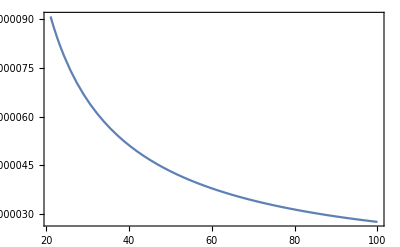
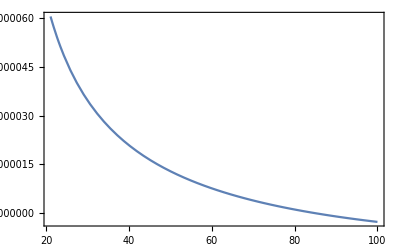
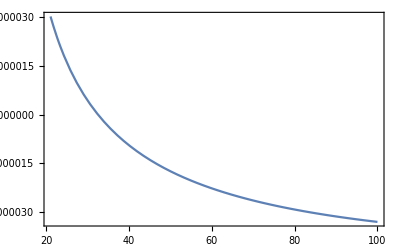

```mathematica
(*np = 1/15*)
{Plot[EqnSpecX[xx/mee,1/15,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/15,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/15,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/15,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/15,0],{xx,80}]
FindRoot[EqnSpecX[xx/mee,1/15,1],{xx,30}]
```

{xx→85.0019}

{xx→32.5328}

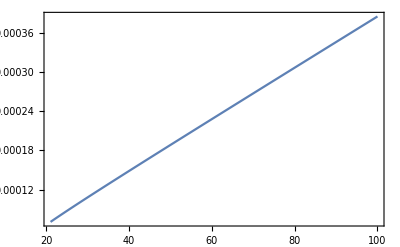
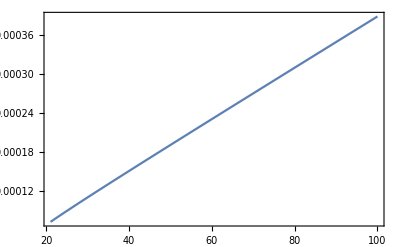
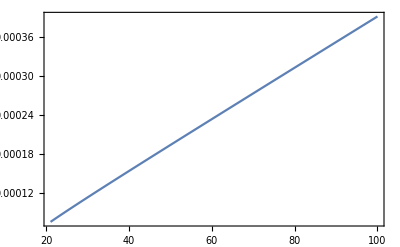
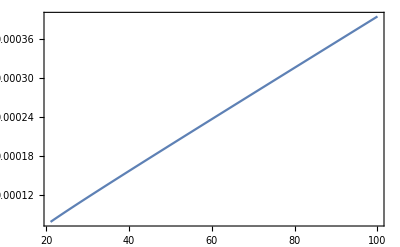

```mathematica
{Plot[EqnSpecTX[xx/mee,1/15,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/15,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/15,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/15,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

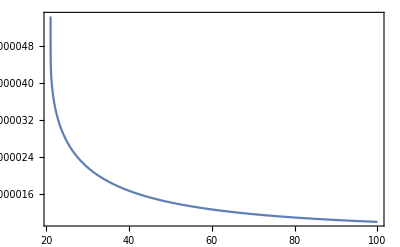
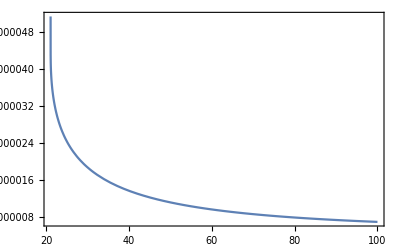
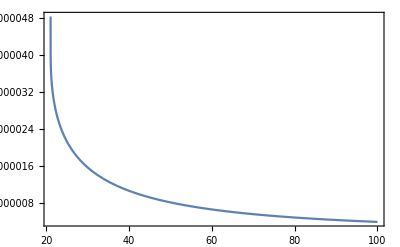
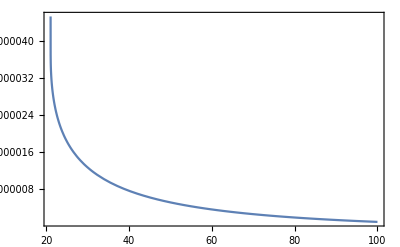

```mathematica
{Plot[EqnSpecY[xx/mee,1/15,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/15,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/15,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/15,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/15,1],{xx,80}]
```

{xx→138.647}

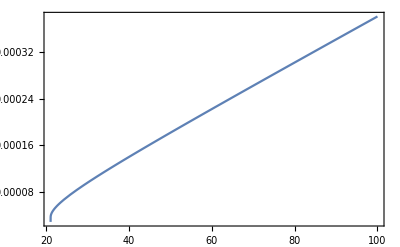
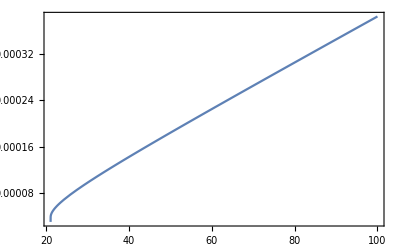
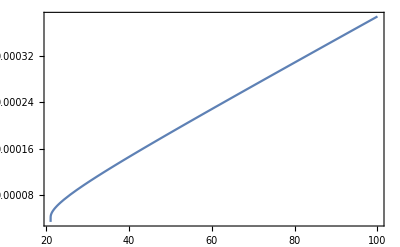
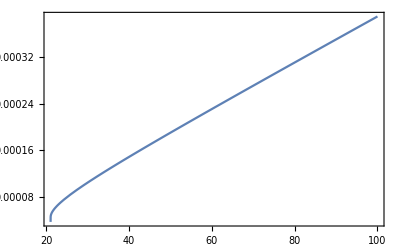

```mathematica
{Plot[EqnSpecTY[xx/mee,1/15,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/15,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/15,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/15,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
tk05s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/15,0]},{x,28,36,0.1}];
tk05sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/15,0]},{x,28,36,0.1}];
```

```mathematica
tk012s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/15,0]},{x,82,88,0.1}];
tk012sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/15,0]},{x,82,88,0.1}];
```

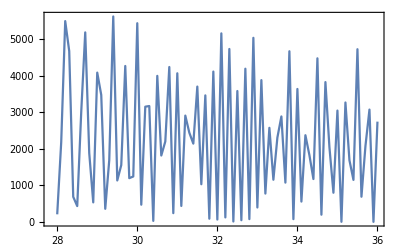
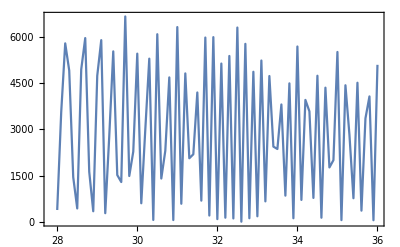
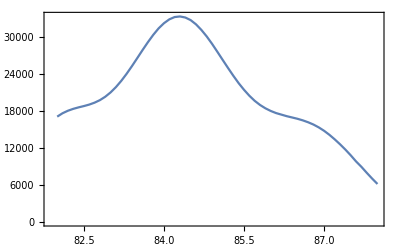
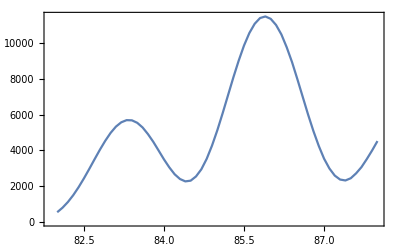

```mathematica
{ListLinePlot[tk05s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk05sm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk012s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk012sm1,Frame->True,Axes->False,PlotRange->Full]}
```

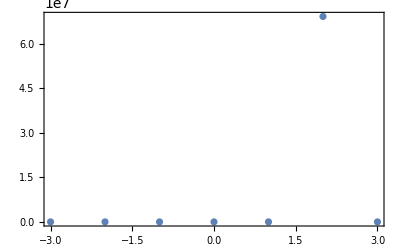
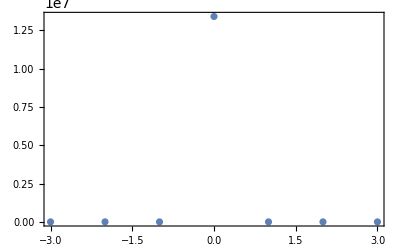

```mathematica
(*хорошее распределение*)
BuildMPlot[85.00194342271016/mee,1/15]
```

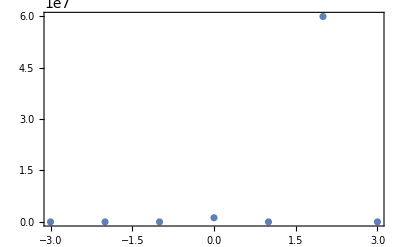
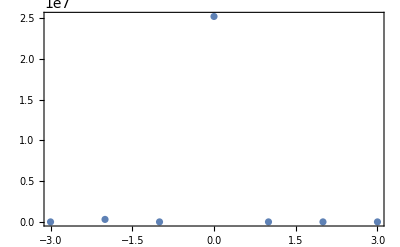

```mathematica
(*тоже хорошее распределение*)
BuildMPlot[86/mee,1/15]
```

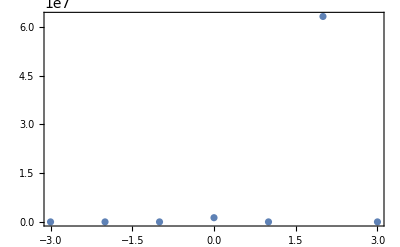
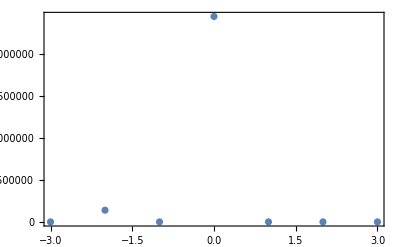

```mathematica
(*тоже приемлемо*)
BuildMPlot[84/mee,1/15]
```

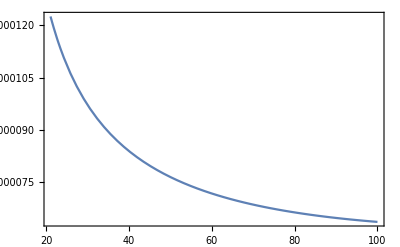
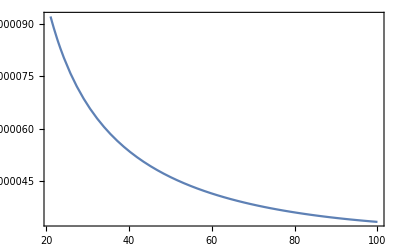
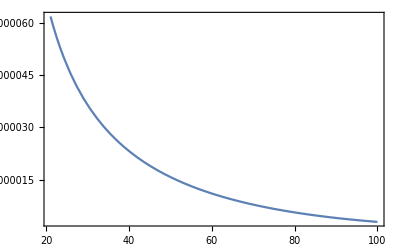
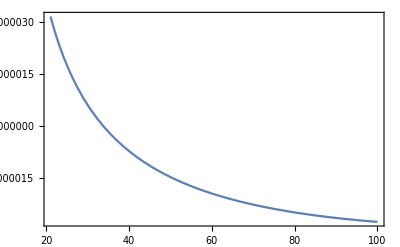

```mathematica
(*np = 1/10*)
{Plot[EqnSpecX[xx/mee,1/10,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/10,1],{xx,30}]
```

{xx→33.8396}

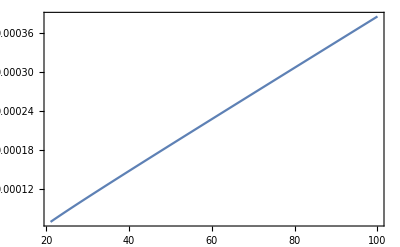
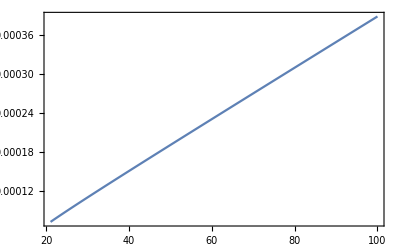
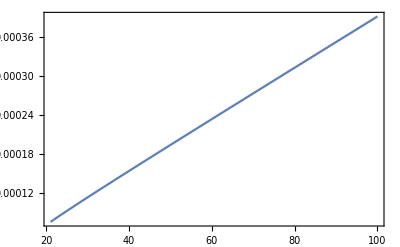
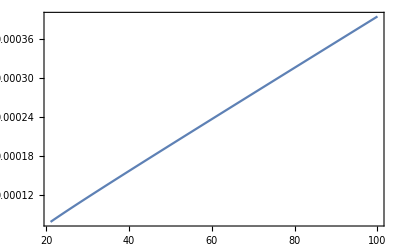

```mathematica
{Plot[EqnSpecTX[xx/mee,1/10,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/10,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/10,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/10,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

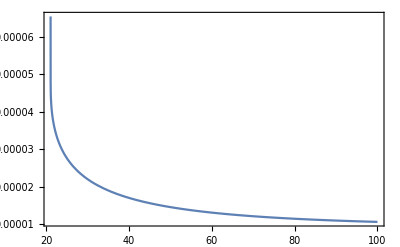
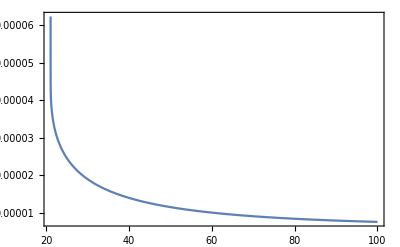
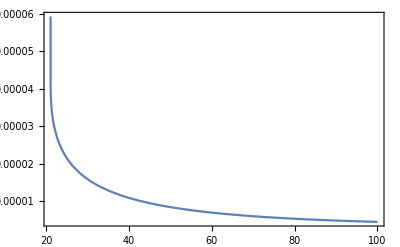
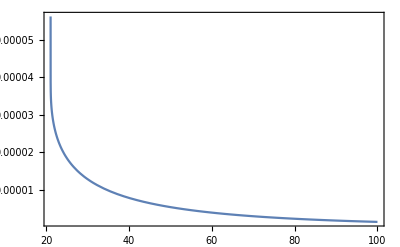

```mathematica
{Plot[EqnSpecY[xx/mee,1/10,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

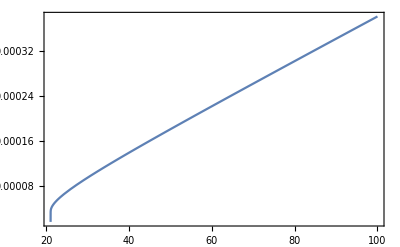
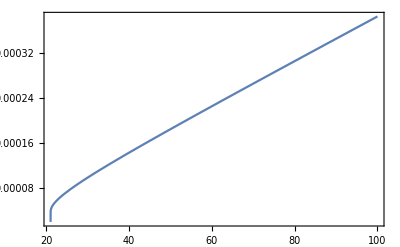
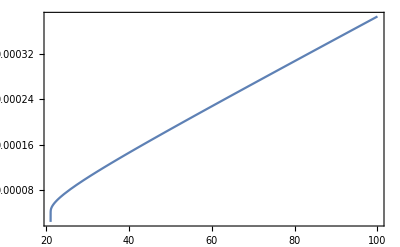
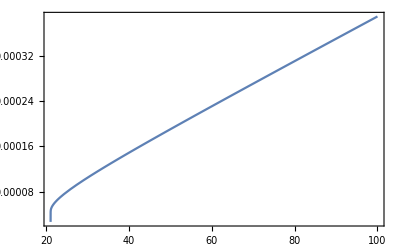

```mathematica
{Plot[EqnSpecTY[xx/mee,1/10,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/10,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/10,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/10,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
tk06s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/10,0]},{x,29,37,0.1}];
tk06sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/10,0]},{x,29,37,0.1}];
```

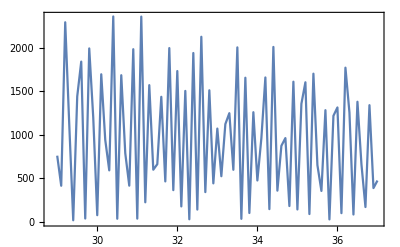
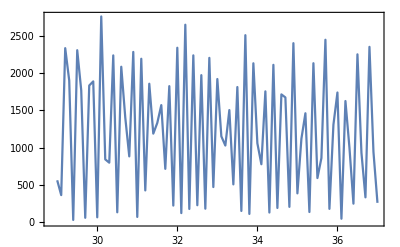

```mathematica
{ListLinePlot[tk06s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk06sm1,Frame->True,Axes->False,PlotRange->Full]}
```

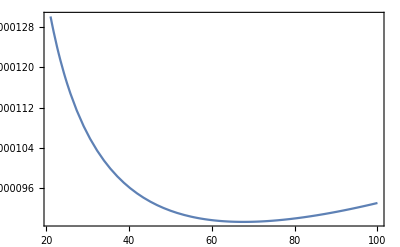
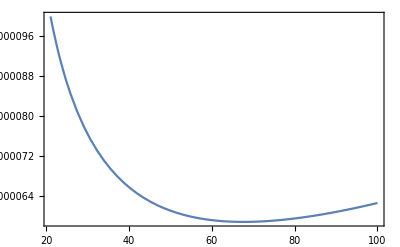
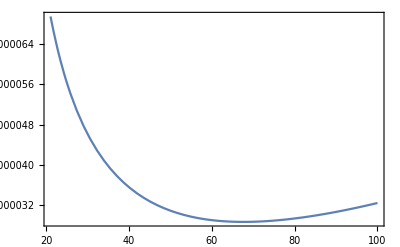
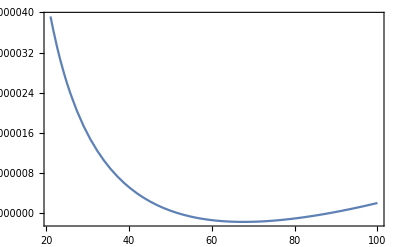

```mathematica
(*np = 1/5*)
{Plot[EqnSpecX[xx/mee,1/5,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/5,1],{xx,60}]
FindRoot[EqnSpecX[xx/mee,1/5,1],{xx,80}]
```

{xx→51.939}

{xx→88.1216}

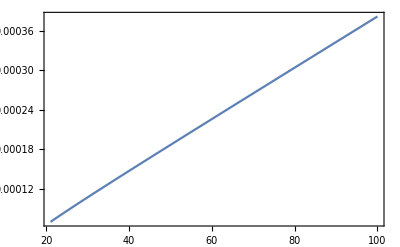
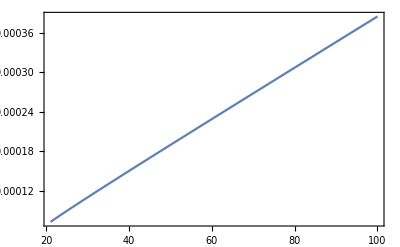
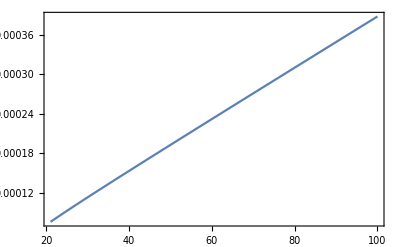
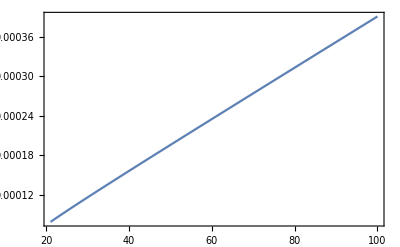

```mathematica
{Plot[EqnSpecTX[xx/mee,1/5,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

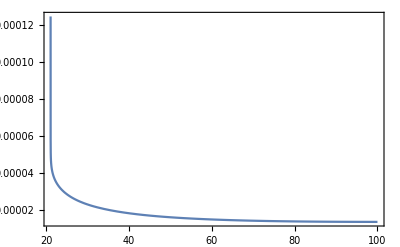
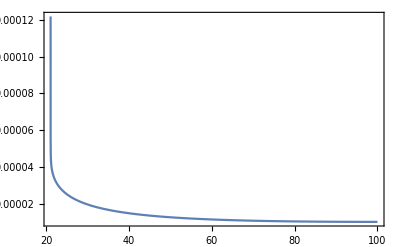
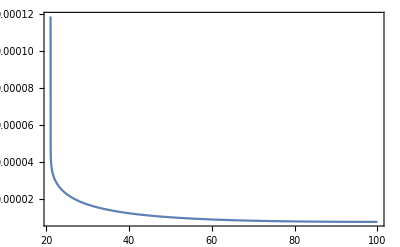
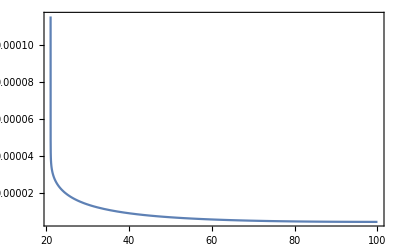

```mathematica
{Plot[EqnSpecY[xx/mee,1/5,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

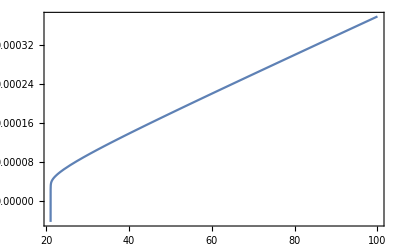
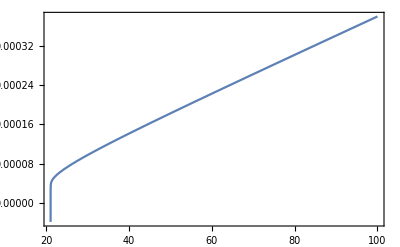
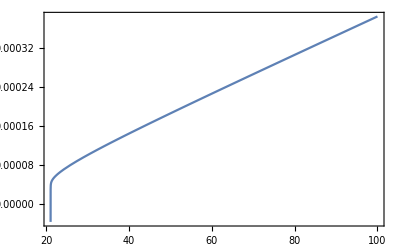
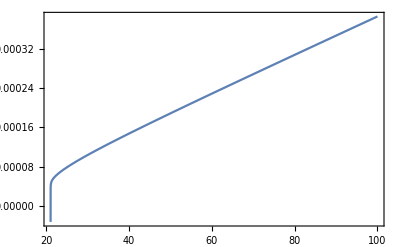

```mathematica
{Plot[EqnSpecTY[xx/mee,1/5,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecTY[xx/mee,1/5,-2],{xx,20}]
FindRoot[EqnSpecTY[xx/mee,1/5,-1],{xx,20}]
FindRoot[EqnSpecTY[xx/mee,1/5,0],{xx,20}]
FindRoot[EqnSpecTY[xx/mee,1/5,1],{xx,20}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{xx→20.-4.59801×10^-14 ⅈ}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{xx→20.-5.0892×10^-14 ⅈ}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{xx→20.-5.59558×10^-14 ⅈ}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{xx→20.-6.11567×10^-14 ⅈ}

```mathematica
tk07s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,48,56,0.1}];
tk07sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,48,56,0.1}];
tk08s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,84,92,0.1}];
tk08sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,84,92,0.1}];
```

```mathematica
tk010s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,16,24,0.1}];
tk010sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,16,24,0.1}];
```

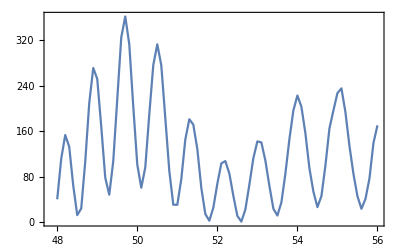
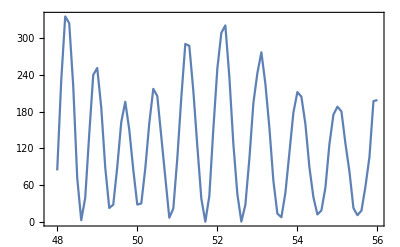
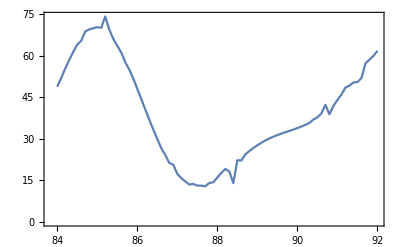
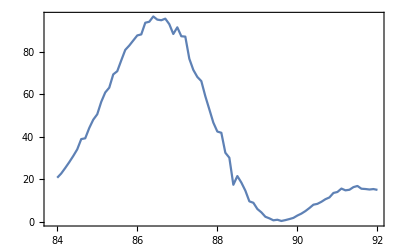

```mathematica
{ListLinePlot[tk07s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk07sm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk08s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk08sm1,Frame->True,Axes->False,PlotRange->Full]}
```

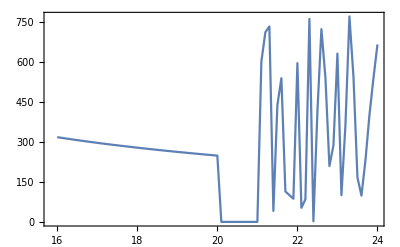
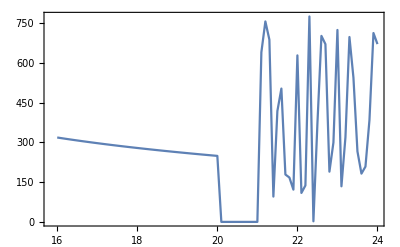

```mathematica
{ListLinePlot[tk010s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk010sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*не хорошее *)
```

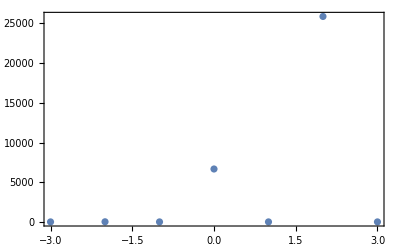
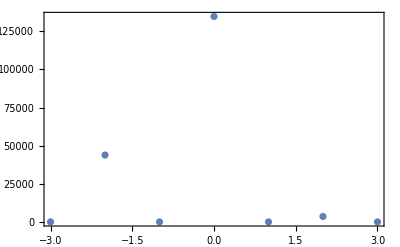

```mathematica
BuildMPlot[88.12158892124798/mee,1/5]
```

```mathematica
(*еще хуже*)
```

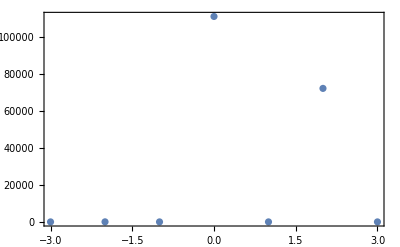
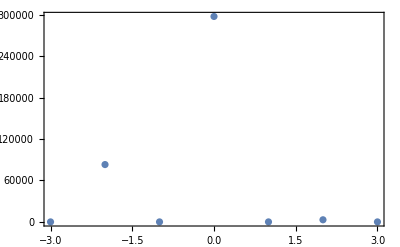

```mathematica
BuildMPlot[86.5/mee,1/5]
```

```mathematica
(*пучки*)
```

```mathematica
(*===================Задаем параметры амплитуды=====================*)
mMax=3;
ss1=-1;(*спиральность фотона*)
kom2=86/mee;(*энергия излучения*)
np11=SetPrecision[1/15,90];(*n_perp*)
(*NN1=20;(*диапазон ненулевых m*)*)
(*NNl=-15;
NNr=15;*)
sigpc=1/(kom2 np11);
Print["Критическое значение поперечного размера пучка: ",sigpc lc 10^4," мкм"]
"Критическое значение поперечного размера пучка: "0.11368645533141207" мкм"
```

Критическое значение поперечного размера пучка: 0.0344034 мкм

Критическое значение поперечного размера пучка: 0.113686 мкм

```mathematica
Np=10^9/(10^4);(*число частиц в пучке*)
sig3=SetPrecision[0.015/lc,90];(*продольный размер. 0.5 ps*)
sigp=SetPrecision[1 10^(-4)/lc,90];(*поперечный размер. 1.25 мкм*)
β3=Sqrt[1-1/γ^2];(*скорость вдоль оси*)
ex=SetPrecision[0.9,90];(*эксцентриситет*)
hx=SetPrecision[0.1,90];(*смещение центра в долях sigp*)
hy=SetPrecision[0.05,90];(*смещение центра в долях sigp*)
ϵy=Sqrt[1-ex^2/2];
ϵx=Sqrt[(1-ex^2/2)/(1-ex^2)];
Print["Продольный размер пучка: ",sig3 lc 10^4," мкм"]
Print["Параметр продольной когерентности: ",kom2 sig3 Sqrt[1-np11^2]]
Print["Параметр размазанности по m: ",kom2 sigp np11]
```

Продольный размер пучка: 150. мкм

Параметр продольной когерентности: 65255.1

Параметр размазанности по m: 29.0669

```mathematica
(*===============Cчитаем амплитуду для разных n_perp и фиксированном kom======================*)
```

```mathematica
npmin=SetPrecision[np11/4,90];(*диапазон npp*)
npmax=SetPrecision[1.5 np11,90];(*диапазон npp*)
npst=10;(*число шагов*)
```

```mathematica
AmplBunchMNpp=Module[{npp2},
Table[{npp2,AmplTwistTab[ss1,kom2,kom2 npp2][[3]]},{npp2,npmin,npmax,(npmax-npmin)/npst}]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 1561.19-3208.54 ⅈ and 2128.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 1938.38-1603.58 ⅈ and 2184.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 2106.62-3133.81 ⅈ and 2149.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 1317.84-1599.31 ⅈ and 2163.97 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 2240.69-2556.81 ⅈ and 2144.96 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 1153.62-1844.94 ⅈ and 2160.83 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 723.196-2664.1 ⅈ and 2047.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 2106.62-3133.81 ⅈ and 2149.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 1098.62-2936.07 ⅈ and 2126.43 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 2240.69-2556.81 ⅈ and 2144.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 1164.22-3061.2 ⅈ and 2059.55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 2076.54-2418.8 ⅈ and 2173.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.06438×10^7}. NIntegrate obtained 361.67-2077.93 ⅈ and 1820.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 1938.38-1603.58 ⅈ and 2184.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 723.196-2664.1 ⅈ and 2047.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 1317.84-1599.31 ⅈ and 2163.97 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 1098.62-2936.07 ⅈ and 2126.43 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 1153.62-1844.94 ⅈ and 2160.83 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 3707.73+11623.5 ⅈ and 3215.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 1019.45+7798.73 ⅈ and 3276.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 2926.2+11442.3 ⅈ and 3222.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 1268.11+7224.2 ⅈ and 3246.07 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 2209.3+11526.6 ⅈ and 3216.34 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 2093.01+6416.48 ⅈ and 3256.16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 5519.38+8175.38 ⅈ and 3215.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 2926.2+11442.3 ⅈ and 3222.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 6217.89+8737.7 ⅈ and 3046.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 2209.3+11526.6 ⅈ and 3216.34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 5845.83+10340.8 ⅈ and 3220.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 815.733+10872.3 ⅈ and 3136.71 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 1019.45+7798.73 ⅈ and 3276.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.06438×10^7}. NIntegrate obtained 5212.66+7532.29 ⅈ and 3262.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 1268.11+7224.2 ⅈ and 3246.07 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 5519.38+8175.38 ⅈ and 3215.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 2093.01+6416.48 ⅈ and 3256.16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 6217.89+8737.7 ⅈ and 3046.82 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained -24839.8+13427.5 ⅈ and 4284.45 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -18187.4+5175.52 ⅈ and 4368.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -25341.5+11155.2 ⅈ and 4323.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -16258.+6519.85 ⅈ and 4354.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -24796.6+8983.91 ⅈ and 4333.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -15214.7+8229.62 ⅈ and 4371.35 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -17165.7+15562.2 ⅈ and 4286.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -25341.5+11155.2 ⅈ and 4323.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -19273.9+16161.9 ⅈ and 4092.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -24796.6+8983.91 ⅈ and 4333.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained -21213.4+15585.4 ⅈ and 4289.62 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained -23413.7+7341.09 ⅈ and 4186.01 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -18187.4+5175.52 ⅈ and 4368.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.06438×10^7}. NIntegrate obtained -15305.+14202.9 ⅈ and 4348.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -16258.+6519.85 ⅈ and 4354.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -17165.7+15562.2 ⅈ and 4286.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -15214.7+8229.62 ⅈ and 4371.35 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -19273.9+16161.9 ⅈ and 4092.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 3735.61-7423.41 ⅈ and 5409.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 2393.07-4475.09 ⅈ and 5495.51 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 4433.93-7202.43 ⅈ and 5435.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 1711.73-4607.43 ⅈ and 5443.05 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 4486.61-6642.65 ⅈ and 5480.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 1250.21-4865.31 ⅈ and 5462.19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 1142.9-7713.99 ⅈ and 5381.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 4433.93-7202.43 ⅈ and 5435.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 1584.59-7942.34 ⅈ and 5374.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 4486.61-6642.65 ⅈ and 5480.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 2202.42-8067.99 ⅈ and 5355.64 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 4278.66-6170.49 ⅈ and 5456.61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 2393.07-4475.09 ⅈ and 5495.51 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.06438×10^7}. NIntegrate obtained 853.535-7182.01 ⅈ and 5432.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 1711.73-4607.43 ⅈ and 5443.05 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 1142.9-7713.99 ⅈ and 5381.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 1250.21-4865.31 ⅈ and 5462.19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 1584.59-7942.34 ⅈ and 5374.59 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained -52670.+41095.3 ⅈ and 6484.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -44483.+29429. ⅈ and 6592.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -53871.4+37965.9 ⅈ and 6586.07 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -41522.3+30643.9 ⅈ and 6572.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -53865.3+35006.9 ⅈ and 6569.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -39473.9+32728.1 ⅈ and 6558.46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -42001.9+43857.7 ⅈ and 6538.89 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -53871.4+37965.9 ⅈ and 6586.07 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -44729.1+44793.5 ⅈ and 6528.53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -53865.3+35006.9 ⅈ and 6569.39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained -47482.9+44664.4 ⅈ and 6438.83 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained -52729.8+32408.1 ⅈ and 6542.36 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -44483.+29429. ⅈ and 6592.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.06438×10^7}. NIntegrate obtained -39687.6+41468.4 ⅈ and 6515.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -41522.3+30643.9 ⅈ and 6572.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -42001.9+43857.7 ⅈ and 6538.89 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -39473.9+32728.1 ⅈ and 6558.46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -44729.1+44793.5 ⅈ and 6528.53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 22401.5+43375.5 ⅈ and 7552.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 15304.2+38963.7 ⅈ and 7732.89 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 20845.6+43936.2 ⅈ and 7671.91 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 15640.9+37432. ⅈ and 7714.36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 19085.5+44063.2 ⅈ and 7754.43 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 16905.9+36080.1 ⅈ and 7647.47 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 23687.1+36609.6 ⅈ and 7658.48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 20845.6+43936.2 ⅈ and 7671.91 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 24564.9+38205.1 ⅈ and 7604.98 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 19085.5+44063.2 ⅈ and 7754.43 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 24654.6+40042.3 ⅈ and 7499.05 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 17076.6+43456. ⅈ and 7657.73 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 15304.2+38963.7 ⅈ and 7732.89 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.06438×10^7}. NIntegrate obtained 22213.9+35284.2 ⅈ and 7595.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 15640.9+37432. ⅈ and 7714.36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 23687.1+36609.6 ⅈ and 7658.48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 16905.9+36080.1 ⅈ and 7647.47 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 24564.9+38205.1 ⅈ and 7604.98 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained -359036.-152099. ⅈ and 8668.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -355918.-149961. ⅈ and 8912.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -357056.-153197. ⅈ and 8786.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -357813.-148115. ⅈ and 8906.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -355615.-154044. ⅈ and 8899.02 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -359669.-146144. ⅈ and 8838.23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -364504.-145468. ⅈ and 8764.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -357056.-153197. ⅈ and 8786.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -363694.-146884. ⅈ and 8782.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -355615.-154044. ⅈ and 8899.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained -362624.-148807. ⅈ and 8553.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained -354566.-153888. ⅈ and 8739.85 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -355918.-149961. ⅈ and 8912.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained -364089.-144740. ⅈ and 8809.38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -357813.-148115. ⅈ and 8906.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -364504.-145468. ⅈ and 8764.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -359669.-146144. ⅈ and 8838.23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -363694.-146884. ⅈ and 8782.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 202265.-52658.6 ⅈ and 9732.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 219163.-54522.9 ⅈ and 10068.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 203619.-55772.2 ⅈ and 9917.92 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 220777.-51437.5 ⅈ and 10133.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 205933.-57347.1 ⅈ and 9989.52 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 220937.-48705.3 ⅈ and 9932.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 209580.-43566.7 ⅈ and 9996.67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 203619.-55772.2 ⅈ and 9917.92 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 205963.-45009.4 ⅈ and 9829.33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 205933.-57347.1 ⅈ and 9989.52 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 203090.-47231.1 ⅈ and 9629.33 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 209798.-57778.2 ⅈ and 9808.23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 219163.-54522.9 ⅈ and 10068.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained 212881.-43136. ⅈ and 9895.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 220777.-51437.5 ⅈ and 10133.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 209580.-43566.7 ⅈ and 9996.67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 220937.-48705.3 ⅈ and 9932.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 205963.-45009.4 ⅈ and 9829.33 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 90360.9-57347.3 ⅈ and 10783.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 108718.-65468.1 ⅈ and 11226.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 91048.-60745.5 ⅈ and 11058.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 110945.-62254.6 ⅈ and 11288.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 92583.4-64215.3 ⅈ and 11142.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 111849.-58950.6 ⅈ and 11072. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 101923.-47828.7 ⅈ and 11083.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 91048.-60745.5 ⅈ and 11058.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 97426.7-48506.8 ⅈ and 10914.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 92583.4-64215.3 ⅈ and 11142.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 93987.3-50709.5 ⅈ and 10672.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 96195.8-66867.3 ⅈ and 10876. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 108718.-65468.1 ⅈ and 11226.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained 106258.-49388. ⅈ and 10976.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 110945.-62254.6 ⅈ and 11288.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 101923.-47828.7 ⅈ and 11083.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 111849.-58950.6 ⅈ and 11072. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 97426.7-48506.8 ⅈ and 10914.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 61321.3-40816.6 ⅈ and 11954.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 80576.9-47667.9 ⅈ and 12409. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 62149.4-44600. ⅈ and 12185.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 82766.6-43941.2 ⅈ and 12450.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 64771.6-47777.1 ⅈ and 12271.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 83659.4-40251.8 ⅈ and 12244.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 72121.6-30178.9 ⅈ and 12250.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained 62149.4-44600. ⅈ and 12185.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 67972.7-31042.9 ⅈ and 12016.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 64771.6-47777.1 ⅈ and 12271.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 64685.4-33709.9 ⅈ and 11707.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 68845.9-50021.2 ⅈ and 11979.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 80576.9-47667.9 ⅈ and 12409. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained 76442.4-31214.2 ⅈ and 12114.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 82766.6-43941.2 ⅈ and 12450.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 72121.6-30178.9 ⅈ and 12250.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 83659.4-40251.8 ⅈ and 12244.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 67972.7-31042.9 ⅈ and 12016.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 51823.7-19145.2 ⅈ and 12999.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 67667.8-15194.5 ⅈ and 13609.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.15095×10^7}. NIntegrate obtained 54438.8-21445.9 ⅈ and 13343.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 67378.-11964.7 ⅈ and 13553.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 57299.4-22159.1 ⅈ and 13339.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 66311.3-9237.28 ⅈ and 13331. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 54418.4-7586.5 ⅈ and 13324. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.15095×10^7}. NIntegrate obtained 54438.8-21445.9 ⅈ and 13343.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 52189.2-9852.44 ⅈ and 13117.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 57299.4-22159.1 ⅈ and 13339.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 50530.5-13051.6 ⅈ and 12818.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 60580.2-22316.3 ⅈ and 13023.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained 67667.8-15194.5 ⅈ and 13609.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained 57603.6-6153.09 ⅈ and 13307.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained 67378.-11964.7 ⅈ and 13553.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 54418.4-7586.5 ⅈ and 13324. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 66311.3-9237.28 ⅈ and 13331. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained 52189.2-9852.44 ⅈ and 13117.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Nnpnt=Length[AmplBunchMNpp[[1,2]]];(*число достоверных m*)
AmplBunchMNppf=Module[{mm,nnp,Nn},Nn=Nnpnt;Table[{{mm,nnp},I^(-mm) AmplBunchMNpp[[1+Round[npst (nnp-npmin)/(npmax-npmin)],2,1+Mod[mm,Nn]]]},{mm,-Floor[Nn/2],Floor[Nn/2]},{nnp,npmin,npmax,(npmax-npmin)/npst}]];
```

```mathematica
Put[AmplBunchMNppf,NotebookDirectory[]<>"XUV"<>"ampl"<>"k0_"<>ToString[Round[kom2 mee]]<>"np_"<>ToString[Round[100 np11]]<>"s_"<>ToString[ss1+1]<>".dat"];(*записываем таблицу в файл*)
```

```mathematica
intAmpl0mnp=Interpolation[Flatten[AmplBunchMNppf,1]];(*строим функцию от (m,np)*)
NNl=-Min[2 mMax,Floor[Nnpnt/2]];NNr=-NNl;
iintAmpl0mnnp[xx_,yy_]:=If[xx>NNr||xx<NNl||yy>npmax||yy<npmin,0,intAmpl0mnp[xx,yy]];(*зануляем вне насчитанной области*)
```

```mathematica
alph[k_]:=If[k==0,1,(ⅇ^(ⅈ k Arg[hx/ϵx-ⅈ hy/ϵy])/(Abs[k]!)(hx^2/ϵx^2+hy^2/ϵy^2)^(Abs[k]/2)+If[EvenQ[k],1/(Abs[k/2]!)((ϵy^-2-ϵx^-2)/2)^Abs[k/2],0])/2^(Abs[k])](*коэффициенты ряда Фурье*)
```

```mathematica
ff1a=Module[{k},ParallelTable[Assuming[x>0,(2^-m x^(2 m-k))/(m!) HypergeometricPFQ[{m-k/2+1/2,m-k/2+1},{m+1,2m-k+1},-2 x^2]//FunctionExpand],{k,NNl-NNr-1,0}]];
ff1[m1_,k_,x1_]:=ff1a[[k-(NNl-NNr-1)+1]]/.{x->x1,m->m1};
ff1[50000,-10,SetPrecision[50000,80]]
ff2a=Module[{k},ParallelTable[Assuming[x>0,(2^(k-m)x^(2 m-k))/((m-k)!) HypergeometricPFQ[{m-k/2+1/2,m-k/2+1},{m-k+1,2m-k+1},-2 x^2]//FunctionExpand],{k,0,NNr-NNl+1}]];
ff2[m1_,k_,x1_]:=ff2a[[k+1]]/.{x->x1,m->m1};
ff2[50000,10,SetPrecision[50000,80]]
```

0.0058842747512157092306408

0.0058851806895738770502371

```mathematica
fg2Dp[m_,k_,x_]:=alph[k] If[k<=0,ff1[m,k,x],If[m≥k,ff2[m,k,x],(-1)^(m+k) k!x^k HypergeometricPFQRegularized[{(k+1)/2,(k+2)/2},{k-m+1,m+1},-2 x^2]]]
fg2D[m_,n_,x_]:=If[m≥0,fg2Dp[m,m-n,x],If[n>=0,Conjugate[fg2Dp[n,n-m,x]],(-1)^(m+n) fg2Dp[-n,m-n,x]]]
φg2D[m_,x_,y1_,nn3_,sg_]:=If[(y1/β3)^2 sg^2/2 +x^2/2 -Abs[m] Log[x]>30,0,Exp[-(y1/β3 )^2 sg^2/2]alph[m](-1)^((m-Abs[m])/2) x^Abs[m] Exp[-x^2/2]]
```

```mathematica
dPbnp[m_?IntegerQ,σ3_?NumberQ,RR_?NumberQ,Np1_?NumberQ,kom1_?NumberQ,nnp_?NumberQ]:=2 α/Pi Np1 Module[{n1,n2,ssu=0,aa},
Do[Do[aa=iintAmpl0mnnp[n1,nnp]Conjugate[iintAmpl0mnnp[n2,nnp]];ssu=ssu+If[Abs[aa]<10^(-30),0,
(fg2D[m-n1,m-n2,kom1 RR nnp]+(Np1-1) φg2D[m-n1,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3] Conjugate[φg2D[m-n2,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3]])aa],{n2,NNl,NNr}],{n1,NNl,NNr}];ssu](*вклады квадратов амплитуд, меньших 10^(-30), отбрасываются*)
```

```mathematica
dProbabTwist1np[mm_?IntegerQ,nnp_?NumberQ]:=2 α/Pi Abs[intAmpl0mnp[mm,nnp]]^2
```

```mathematica
(*===============Cчитаем амплитуду для разных k0 и фиксированном n_perp======================*)
```

```mathematica
komin=SetPrecision[kom2/4,90];(*диапазон ko*)
komax=SetPrecision[1.5 kom2,90];(*диапазон ko*)
kost=10;(*число шагов*)
```

```mathematica
AmplBunchMKo=Module[{koo},
Table[{koo,AmplTwistTab[ss1,koo,koo np11][[3]]},{koo,komin,komax,(komax-komin)/kost}]];(*таблица амплитуд по k0 при фиксированном nperp=np11*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.08011×10^7}. NIntegrate obtained -289.781-5742.59 ⅈ and 62.3395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.05426×10^7}. NIntegrate obtained -6635.42-10937.2 ⅈ and 61.9793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.19594×10^7}. NIntegrate obtained -1952.16-5237.03 ⅈ and 62.3377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained -5816.2-12461.6 ⅈ and 61.7933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.62098×10^7}. NIntegrate obtained -3680.43-5405.14 ⅈ and 62.3727 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -4475.35-13557.3 ⅈ and 61.7391 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 1533.26-11741.6 ⅈ and 62.3202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.19594×10^7}. NIntegrate obtained -1952.16-5237.03 ⅈ and 62.3377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.76265×10^7}. NIntegrate obtained 2037.33-10090.4 ⅈ and 62.3785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.62098×10^7}. NIntegrate obtained -3680.43-5405.14 ⅈ and 62.3727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.40021×10^7}. NIntegrate obtained 1868.91-8370.69 ⅈ and 62.3882 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.04601×10^7}. NIntegrate obtained -5210.11-6221.11 ⅈ and 62.4055 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.05426×10^7}. NIntegrate obtained -6635.42-10937.2 ⅈ and 61.9793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.70232×10^6}. NIntegrate obtained 434.138-13074.7 ⅈ and 62.1925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained -5816.2-12461.6 ⅈ and 61.7933 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 1533.26-11741.6 ⅈ and 62.3202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -4475.35-13557.3 ⅈ and 61.7391 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.76265×10^7}. NIntegrate obtained 2037.33-10090.4 ⅈ and 62.3785 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.7158×10^7}. NIntegrate obtained -4319.99+7156.56 ⅈ and 2051.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.99916×10^7}. NIntegrate obtained 4352.01+16040.5 ⅈ and 2054.26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.63484×10^7}. NIntegrate obtained -1476.11+6768.08 ⅈ and 2052.68 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.9182×10^7}. NIntegrate obtained 2559.26+18085.3 ⅈ and 2052.57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.42683×10^7}. NIntegrate obtained 1268.2+7374.92 ⅈ and 2054.78 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.71018×10^7}. NIntegrate obtained 55.7045+19399.9 ⅈ and 2051.84 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained -9107.45+15521. ⅈ and 2047.45 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.63484×10^7}. NIntegrate obtained -1476.11+6768.08 ⅈ and 2052.68 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.21358×10^6}. NIntegrate obtained -9417.92+13009.6 ⅈ and 2048.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.42683×10^7}. NIntegrate obtained 1268.2+7374.92 ⅈ and 2054.78 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.93469×10^7}. NIntegrate obtained -8618.29+10536.9 ⅈ and 2049.77 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.34587×10^7}. NIntegrate obtained 3493.21+8883.23 ⅈ and 2055.76 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.99916×10^7}. NIntegrate obtained 4352.01+16040.5 ⅈ and 2054.26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.41033×10^7}. NIntegrate obtained -7736.24+17689.1 ⅈ and 2047.53 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.9182×10^7}. NIntegrate obtained 2559.26+18085.3 ⅈ and 2052.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained -9107.45+15521. ⅈ and 2047.45 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.71018×10^7}. NIntegrate obtained 55.7045+19399.9 ⅈ and 2051.84 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.21358×10^6}. NIntegrate obtained -9417.92+13009.6 ⅈ and 2048.06 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.78477×10^7}. NIntegrate obtained 5427.89-9536.1 ⅈ and 13161.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.57714×10^6}. NIntegrate obtained 9193.57-3570.12 ⅈ and 13572.7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.53364×10^7}. NIntegrate obtained 6556.77-9426.41 ⅈ and 13347.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 8003.32-2635.79 ⅈ and 13539.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.04975×10^7}. NIntegrate obtained 7952.97-9246.61 ⅈ and 13135.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.79153×10^6}. NIntegrate obtained 6472.2-1988.68 ⅈ and 13165. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.38673×10^6}. NIntegrate obtained 2586.74-5120.78 ⅈ and 13163.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.53364×10^7}. NIntegrate obtained 6556.77-9426.41 ⅈ and 13347.4 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.91445×10^7}. NIntegrate obtained 2012.96-5942.93 ⅈ and 13287.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.04975×10^7}. NIntegrate obtained 7952.97-9246.61 ⅈ and 13135.4 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.66333×10^7}. NIntegrate obtained 2604.58-7773.47 ⅈ and 13255.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 8980.-7871.26 ⅈ and 13615.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.57714×10^6}. NIntegrate obtained 9193.57-3570.12 ⅈ and 13572.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.45268×10^7}. NIntegrate obtained 2812.1-3336.62 ⅈ and 13305.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained 8003.32-2635.79 ⅈ and 13539.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.38673×10^6}. NIntegrate obtained 2586.74-5120.78 ⅈ and 13163.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.79153×10^6}. NIntegrate obtained 6472.2-1988.68 ⅈ and 13165. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.91445×10^7}. NIntegrate obtained 2012.96-5942.93 ⅈ and 13287.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.11047×10^7}. NIntegrate obtained -17552.+2752.71 ⅈ and 15923.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.30539×10^7}. NIntegrate obtained -10025.6-931.856 ⅈ and 15939.7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.62472×10^7}. NIntegrate obtained -11174.2+540.852 ⅈ and 15925.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.70232×10^6}. NIntegrate obtained -18980.2+1144.42 ⅈ and 16021. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.16107×10^7}. NIntegrate obtained -11457.4+2052.46 ⅈ and 16047.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.40659×10^7}. NIntegrate obtained -19423.7-785.107 ⅈ and 15904.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.35599×10^7}. NIntegrate obtained -15634.1-5936.09 ⅈ and 15974.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.62472×10^7}. NIntegrate obtained -11174.2+540.852 ⅈ and 15925.3 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.67532×10^7}. NIntegrate obtained -13359.3-5134.33 ⅈ and 16064.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.16107×10^7}. NIntegrate obtained -11457.4+2052.46 ⅈ and 16047.1 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.55201×10^7}. NIntegrate obtained -12431.4-4461.42 ⅈ and 16058.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.3781×10^7}. NIntegrate obtained -12647.+2731.98 ⅈ and 16086. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.11047×10^7}. NIntegrate obtained -17552.+2752.71 ⅈ and 15923.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.19632×10^6}. NIntegrate obtained -17468.8-5220.15 ⅈ and 15786.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.70232×10^6}. NIntegrate obtained -18980.2+1144.42 ⅈ and 16021. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.35599×10^7}. NIntegrate obtained -15634.1-5936.09 ⅈ and 15974.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.40659×10^7}. NIntegrate obtained -19423.7-785.107 ⅈ and 15904.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.67532×10^7}. NIntegrate obtained -13359.3-5134.33 ⅈ and 16064.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.09287×10^7}. NIntegrate obtained 36432.2-7358.84 ⅈ and 5655.64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.55315×10^6}. NIntegrate obtained 29121.9-7702.52 ⅈ and 5908.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 29814.6-8163.1 ⅈ and 5538.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.09287×10^7}. NIntegrate obtained 35596.1-5098.07 ⅈ and 5825.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.64946×10^7}. NIntegrate obtained 29350.4-9210.96 ⅈ and 5617.55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {707588.}. NIntegrate obtained 35682.4-3775.27 ⅈ and 6198.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.02203×10^7}. NIntegrate obtained 29786.9-1473.82 ⅈ and 5950.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 29814.6-8163.1 ⅈ and 5538.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.48304×10^7}. NIntegrate obtained 29003.8-2381.14 ⅈ and 5519.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.64946×10^7}. NIntegrate obtained 29350.4-9210.96 ⅈ and 5617.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.21618×10^7}. NIntegrate obtained 28614.4-3166.49 ⅈ and 5626.38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.10711×10^6}. NIntegrate obtained 32127.-9558.34 ⅈ and 5727.78 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.09287×10^7}. NIntegrate obtained 36432.2-7358.84 ⅈ and 5655.64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26155×10^6}. NIntegrate obtained 32045.7-1500.88 ⅈ and 5710.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.09287×10^7}. NIntegrate obtained 35596.1-5098.07 ⅈ and 5825.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.02203×10^7}. NIntegrate obtained 29786.9-1473.82 ⅈ and 5950.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {707588.}. NIntegrate obtained 35682.4-3775.27 ⅈ and 6198.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.48304×10^7}. NIntegrate obtained 29003.8-2381.14 ⅈ and 5519.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.93469×10^7}. NIntegrate obtained -10919.6-7730.44 ⅈ and 10108.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4122×10^7}. NIntegrate obtained -14318.7-7930.73 ⅈ and 10376. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.89421×10^7}. NIntegrate obtained -11005.9-6599.02 ⅈ and 10181.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.77277×10^7}. NIntegrate obtained -14141.2-8210.46 ⅈ and 10313. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.40021×10^7}. NIntegrate obtained -13134.7-9462.41 ⅈ and 10057.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.9227×10^7}. NIntegrate obtained -11244.7-6607.09 ⅈ and 10454. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.94856×10^7}. NIntegrate obtained -11211.2-9435.64 ⅈ and 9802.83 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.89421×10^7}. NIntegrate obtained -11005.9-6599.02 ⅈ and 10181.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.9182×10^7}. NIntegrate obtained -9977.11-9581.83 ⅈ and 10235.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.9227×10^7}. NIntegrate obtained -11244.7-6607.09 ⅈ and 10454. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.74356×10^6}. NIntegrate obtained -9750.77-9295.47 ⅈ and 10446.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.55014×10^7}. NIntegrate obtained -11791.3-6536.77 ⅈ and 10449.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4122×10^7}. NIntegrate obtained -14318.7-7930.73 ⅈ and 10376. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.41671×10^7}. NIntegrate obtained -12303.2-10643.1 ⅈ and 10357.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.77277×10^7}. NIntegrate obtained -14141.2-8210.46 ⅈ and 10313. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.94856×10^7}. NIntegrate obtained -11211.2-9435.64 ⅈ and 9802.83 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.40021×10^7}. NIntegrate obtained -13134.7-9462.41 ⅈ and 10057.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.9182×10^7}. NIntegrate obtained -9977.11-9581.83 ⅈ and 10235.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained -359036.-152099. ⅈ and 8668.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -355918.-149961. ⅈ and 8912.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -357056.-153197. ⅈ and 8786.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -357813.-148115. ⅈ and 8906.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -355615.-154044. ⅈ and 8899.02 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -359669.-146144. ⅈ and 8838.23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -364504.-145468. ⅈ and 8764.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10299×10^7}. NIntegrate obtained -357056.-153197. ⅈ and 8786.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -363694.-146884. ⅈ and 8782.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -355615.-154044. ⅈ and 8899.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.17383×10^7}. NIntegrate obtained -362624.-148807. ⅈ and 8553.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained -354566.-153888. ⅈ and 8739.85 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.79114×10^7}. NIntegrate obtained -355918.-149961. ⅈ and 8912.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4793×10^7}. NIntegrate obtained -364089.-144740. ⅈ and 8809.38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.18956×10^7}. NIntegrate obtained -357813.-148115. ⅈ and 8906.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained -364504.-145468. ⅈ and 8764.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -359669.-146144. ⅈ and 8838.23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.22817×10^7}. NIntegrate obtained -363694.-146884. ⅈ and 8782.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.49767×10^7}. NIntegrate obtained -7030.2-32836.8 ⅈ and 1965.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.71018×10^7}. NIntegrate obtained -17800.7-40580.4 ⅈ and 1973.23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.45081×10^7}. NIntegrate obtained -8239.08-30445.6 ⅈ and 1982.31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.67158×10^7}. NIntegrate obtained -15114.5-41463.9 ⅈ and 2080.43 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.12884×10^7}. NIntegrate obtained -12234.8-41313.8 ⅈ and 1966.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.43882×10^7}. NIntegrate obtained -10406.6-28686.8 ⅈ and 1957.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.19632×10^6}. NIntegrate obtained -20555.3-31028.5 ⅈ and 1993.26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.67158×10^7}. NIntegrate obtained -15114.5-41463.9 ⅈ and 2080.43 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.78102×10^7}. NIntegrate obtained -21374.7-33608. ⅈ and 1908.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.12884×10^7}. NIntegrate obtained -12234.8-41313.8 ⅈ and 1966.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.69033×10^6}. NIntegrate obtained -21227.4-36320.4 ⅈ and 1987.69 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {909987.}. NIntegrate obtained -9632.08-40151.6 ⅈ and 1963.69 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.49767×10^7}. NIntegrate obtained -7030.2-32836.8 ⅈ and 1965.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.23757×10^6}. NIntegrate obtained -18674.3-29132.5 ⅈ and 1941.66 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.45081×10^7}. NIntegrate obtained -8239.08-30445.6 ⅈ and 1982.31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.19632×10^6}. NIntegrate obtained -20555.3-31028.5 ⅈ and 1993.26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.43882×10^7}. NIntegrate obtained -10406.6-28686.8 ⅈ and 1957.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.78102×10^7}. NIntegrate obtained -21374.7-33608. ⅈ and 1908.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.74356×10^6}. NIntegrate obtained 21908.8-12905.1 ⅈ and 2025.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.36611×10^7}. NIntegrate obtained 17472.8-5840.89 ⅈ and 2087.77 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.14534×10^7}. NIntegrate obtained 22539.-11589.1 ⅈ and 2052.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.91258×10^7}. NIntegrate obtained 15672.8-6008.43 ⅈ and 2099.31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.29901×10^7}. NIntegrate obtained 22554.8-9935.95 ⅈ and 2115.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained 14463.4-6466.19 ⅈ and 2046.55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained 15610.6-12794.8 ⅈ and 2026.76 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.14534×10^7}. NIntegrate obtained 22539.-11589.1 ⅈ and 2052.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.91445×10^7}. NIntegrate obtained 17353.6-13869.5 ⅈ and 2027.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.29901×10^7}. NIntegrate obtained 22554.8-9935.95 ⅈ and 2115.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.45081×10^7}. NIntegrate obtained 19161.7-14089.9 ⅈ and 2074.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.6817×10^7}. NIntegrate obtained 21891.2-8211.43 ⅈ and 2154.33 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.36611×10^7}. NIntegrate obtained 17472.8-5840.89 ⅈ and 2087.77 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.76078×10^7}. NIntegrate obtained 14466.2-11428.3 ⅈ and 2010.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.91258×10^7}. NIntegrate obtained 15672.8-6008.43 ⅈ and 2099.31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained 15610.6-12794.8 ⅈ and 2026.76 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained 14463.4-6466.19 ⅈ and 2046.55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.91445×10^7}. NIntegrate obtained 17353.6-13869.5 ⅈ and 2027.61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -3081.85+21330.8 ⅈ and 262.756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.77277×10^7}. NIntegrate obtained -5780.74+13877.6 ⅈ and 271.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.29714×10^7}. NIntegrate obtained -4636.6+21042.2 ⅈ and 272.905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.8676×10^7}. NIntegrate obtained -4448.01+12826.3 ⅈ and 265.466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.38184×10^7}. NIntegrate obtained -5977.67+20098.2 ⅈ and 271.813 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.9733×10^7}. NIntegrate obtained -2895.16+12433.6 ⅈ and 270.518 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.64236×10^6}. NIntegrate obtained 1062.97+16810.9 ⅈ and 264.572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.29714×10^7}. NIntegrate obtained -4636.6+21042.2 ⅈ and 272.905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.9062×10^7}. NIntegrate obtained 757.543+18604.2 ⅈ and 269.21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.38184×10^7}. NIntegrate obtained -5977.67+20098.2 ⅈ and 271.813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.01191×10^7}. NIntegrate obtained -140.68+20024.9 ⅈ and 263.515 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {403991.}. NIntegrate obtained -6762.94+18659.3 ⅈ and 270.99 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.77277×10^7}. NIntegrate obtained -5780.74+13877.6 ⅈ and 271.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.70568×10^7}. NIntegrate obtained 789.503+15190.3 ⅈ and 269.425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.8676×10^7}. NIntegrate obtained -4448.01+12826.3 ⅈ and 265.466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.64236×10^6}. NIntegrate obtained 1062.97+16810.9 ⅈ and 264.572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.9733×10^7}. NIntegrate obtained -2895.16+12433.6 ⅈ and 270.518 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.9062×10^7}. NIntegrate obtained 757.543+18604.2 ⅈ and 269.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Nnpnt1=Length[AmplBunchMKo[[1,2]]];(*число достоверных m*)
AmplBunchMKof=Module[{mm,koo,Nn},Nn=Nnpnt1;Table[{{mm,koo},I^(-mm) AmplBunchMKo[[1+Round[kost (koo-komin)/(komax-komin)],2,1+Mod[mm,Nn]]]},{mm,-Floor[Nn/2],Floor[Nn/2]},{koo,komin,komax,(komax-komin)/kost}]];
```

```mathematica
Put[AmplBunchMKof,NotebookDirectory[]<>"XUV"<>"ampl"<>"np_"<>ToString[Round[100 np11]]<>"ko_"<>ToString[Round[kom2 mee]]<>"s_"<>ToString[ss1+1]<>".dat"];(*записываем таблицу в файл*)
```

```mathematica
intAmpl0mko=Interpolation[Flatten[AmplBunchMKof,1]];(*строим функцию от (m,ko)*)
NNl1=-Min[2 mMax,Floor[Nnpnt1/2]];NNr1=-NNl1;
iintAmpl0mkoo[xx_,yy_]:=If[xx>NNr1||xx<NNl1||yy>komax||yy<komin,0,intAmpl0mko[xx,yy]];(*зануляем вне насчитанной области*)
```

```mathematica
dPbko[m_?IntegerQ,σ3_?NumberQ,RR_?NumberQ,Np1_?NumberQ,kom1_?NumberQ,nnp_?NumberQ]:=2 α/Pi Np1 Module[{n1,n2,ssu=0,aa},
Do[Do[aa=iintAmpl0mkoo[n1,kom1]Conjugate[iintAmpl0mkoo[n2,kom1]];ssu=ssu+If[Abs[aa]<10^(-30),0,
(fg2D[m-n1,m-n2,kom1 RR nnp]+(Np1-1) φg2D[m-n1,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3] Conjugate[φg2D[m-n2,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3]])aa],{n2,NNl1,NNr1}],{n1,NNl1,NNr1}];ssu](*вклады квадратов амплитуд, меньших 10^(-30), отбрасываются*)
```

```mathematica
dProbabTwist1ko[mm_?IntegerQ,koo_?NumberQ]:=2 α/Pi Abs[intAmpl0mko[mm,koo]]^2
```

```mathematica
(*+++++++++++++++plots++++++++++++++++*)
```

```mathematica
BuildBeamEnergyPlot[k000_,np11_]:=Module[{bkos1mm2,bkos1mm1,bkos1m0,bkos1m1,bkos1m2},
bkos1mm2=ParallelTable[{x,Re[dPbko[-2,sig3,sigp,Np,x/mee,np11]]},{x,k000 mee-4,k000 mee+4,0.05}];
bkos1mm1=ParallelTable[{x,Re[dPbko[-1,sig3,sigp,Np,x/mee,np11]]},{x,k000 mee-4,k000 mee+4,0.05}];
bkos1m0=ParallelTable[{x,Re[dPbko[0,sig3,sigp,Np,x/mee,np11]]},{x,k000 mee-4,k000 mee+4,0.05}];
bkos1m1=ParallelTable[{x,Re[dPbko[1,sig3,sigp,Np,x/mee,np11]]},{x,k000 mee-4,k000 mee+4,0.05}];
bkos1m2=ParallelTable[{x,Re[dPbko[2,sig3,sigp,Np,x/mee,np11]]},{x,k000 mee-4,k000 mee+4,0.05}];
Print["Пучковые графики по энергии, в окрестности ",kom2 mee, "при np=", Round[np11*1000]/1000, " s=", ss1];
{ListLinePlot[bkos1mm2,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1mm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1m0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1m1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1m2,Frame->True,Axes->False,PlotRange->Full]}
]
```

```mathematica
BuildBeamNPPlot[k000_,np11_]:=Module[{bnps1mm2,bnps1mm1,bnps1m0,bnps1m1,bnps1m2},
bnps1mm2=ParallelTable[{x,Re[dPbnp[-2,sig3,sigp,Np,kom2,x]]},{x,npmin,npmax,0.001}];
bnps1mm1=ParallelTable[{x,Re[dPbnp[-1,sig3,sigp,Np,kom2,x]]},{x,npmin,npmax,0.001}];
bnps1m0=ParallelTable[{x,Re[dPbnp[0,sig3,sigp,Np,kom2,x]]},{x,npmin,npmax,0.001}];
bnps1m1=ParallelTable[{x,Re[dPbnp[1,sig3,sigp,Np,kom2,x]]},{x,npmin,npmax,0.001}];
bnps1m2=ParallelTable[{x,Re[dPbnp[2,sig3,sigp,Np,kom2,x]]},{x,npmin,npmax,0.001}];
Print["Пучковые графики по np, в окрестности ",Round[np11*1000]/1000, "при ko=", kom2 mee " s=", ss1,"для m: -2, -1, 0, 1, 2"];
{ListLinePlot[bnps1mm2,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1mm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1m0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1m1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1m2,Frame->True,Axes->False,PlotRange->Full]}
]
```

```mathematica
Build1ParticleEnergyPlot[]:=Module[{},
Print["Одночастичные графики графики по ko, в окрестности ",kom2 mee, "при np=",  Round[np11*1000]/1000," s=", ss1,"для m: -2, -1, 0, 1, 2"];
{Plot[dProbabTwist1ko[-2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[-1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full], 
Plot[dProbabTwist1ko[0, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full]}]
```

```mathematica
Build1ParticleNPPLot[]:=Module[{},
Print["Одночастичные графики графики по np, в окрестности ",Round[np11*1000]/1000, "при ko=", kom2 mee ," s=", ss1,"для m: -2, -1, 0, 1, 2"];
{Plot[dProbabTwist1np[-2, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[-1, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[0, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[1, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[2, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full]}
]
```

```mathematica
(*ko 86, np 1/15, s=-1*)
BuildBeamEnergyPlot[kom2,np11]
BuildBeamNPPlot[kom2,np11]
Build1ParticleEnergyPlot[]
Build1ParticleNPPLot[]
```

```mathematica
(*ko 86, np 1/15, s=1*)
```

Пучковые графики по энергии, в окрестности 86.при np=67/1000 s=1

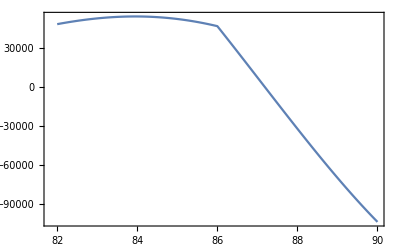
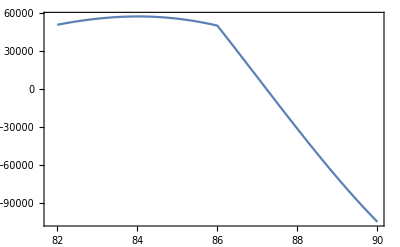
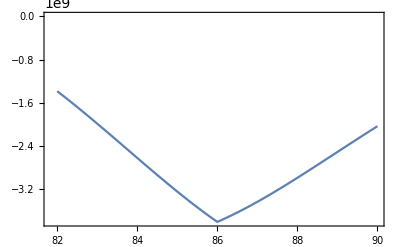
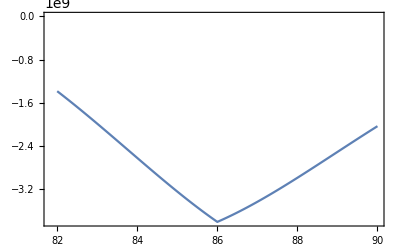
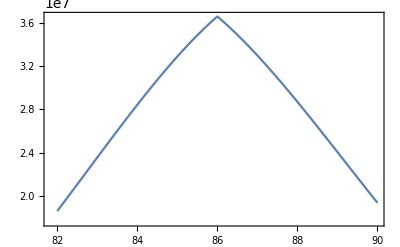

```mathematica
BuildBeamEnergyPlot[kom2,np11]
```

```mathematica
BuildBeamNPPlot[kom2,np11]
```

Пучковые графики по np, в окрестности 67/1000 при ko=86.  s=1для m: -2, -1, 0, 1, 2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Одночастичные графики графики по ko, в окрестности 86.при np=67/1000 s=1для m: -2, -1, 0, 1, 2

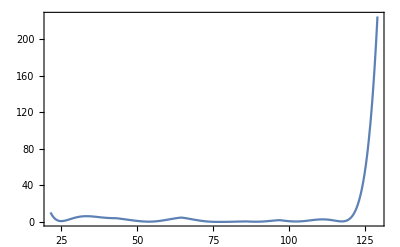
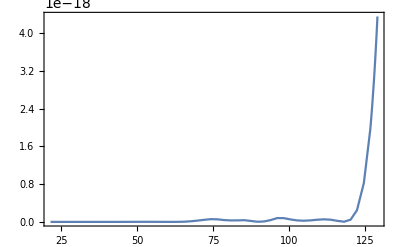
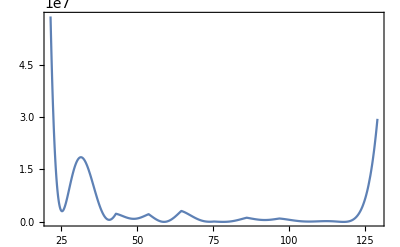
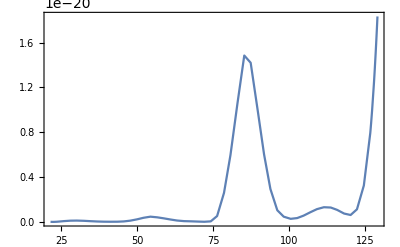
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Build1ParticleEnergyPlot[]
```

```mathematica
Build1ParticleNPPLot[]
```

Одночастичные графики графики по np, в окрестности 67/1000 при ko=86. s=1для m: -2, -1, 0, 1, 2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*ko 85,np 1/15,s=1*)
```

```mathematica
BuildBeamEnergyPlot[kom2,np11]
```

Пучковые графики по энергии, в окрестности 85.0019при np=7/100 s=1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BuildBeamNPPlot[kom2,np11]
```

Пучковые графики по np, в окрестности 67/1000 при ko=85.0019  s=1для m: -2, -1, 0, 1, 2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Build1ParticleEnergyPlot[]
```

Одночастичные графики графики по ko, в окрестности 85.0019при np=67/1000 s=1для m: -2, -1, 0, 1, 2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Build1ParticleNPPLot[]
```

Одночастичные графики графики по np, в окрестности 67/1000 при ko=85.0019 s=1для m: -2, -1, 0, 1, 2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}